```mathematica
ClearAll["Global`*"]
```

## Helper Functions

### Functions for extracting information from chromosomes

```mathematica
(* Function (and its reverse) to turn chromosome into a partition. E.g. {1,1,2,1,3}-> {{1,2,4},{3},{5}} *)
ChromosomeToPartition[chromosome_]:=GatherBy[List~MapIndexed~chromosome,First][[All,All,2,1]];
PartitionToChromosome[partition_]:=Table[FirstPosition[partition,i]⟦1⟧, {i,1,Length[Flatten[partition]]}]

(* Function to compute fitness of chromosome *)
Fitness[network_, chromosome_]:=GraphAssortativity[network, ChromosomeToPartition[chromosome],"Normalized"->False];

(* Function to count the number of communities represented by a chromosome *)
CommunityCount[chromosome_]:=CountDistinct[chromosome];

(* Relabels the communities represented by a chromosome such that first community has label 0 and last community n-1 where n is the number of communities *)
RelabelChromosome[chromosome_]:=Module[{MyCommunityLabels=DeleteDuplicates[chromosome], relabeledChromosome=chromosome},
Table[relabeledChromosome =relabeledChromosome/.{RankedMin[MyCommunityLabels,pos]->pos-1},{pos,Length[MyCommunityLabels]}];
Return[relabeledChromosome];
];
```

### Functions for plotting the network

```mathematica
(* Plot graph with blue links and nodes *)
MyGraphPlot[g_] :=GraphPlot[g,  VertexRenderingFunction-> ({LightBlue, EdgeForm[Blue], Disk[#, .04]}&), EdgeRenderingFunction->({LightBlue, Line[#]}&), ImageSize->Large];

(* Plot graph with different node colors for each community and optionally color gradient links *)
MyCommunityPlot[g_, chromosome_, drawGradientEdges_:True]:=Module[{CommunityHue,VertexOptions , EdgeOptions},

(* Defines hue value for a node. Use a transformation in order to avoid the color yellow which can be hardly recognized on the white background *)
(*CommunityHue[node_]:=chromosome⟦node⟧ 0.8((VertexCount[g] -1)/VertexCount[g])+1/4;*)
(*CommunityHue[node_]:=chromosome⟦node⟧ /4;*)

(* Defines hue value for a node *)
CommunityHue[node_]:=chromosome⟦node⟧ /CommunityCount[chromosome];

(* Draw nodes as circles *)
(*VertexOptions =  VertexRenderingFunction-> ({Hue[CommunityHue[#2], .1], EdgeForm[Hue[CommunityHue[#2]]], Disk[#1, .04], Black, Text[#2,#1 + {0,0.2}]}&);*)
VertexOptions =  VertexRenderingFunction-> ({Hue[CommunityHue[#2], .1], EdgeForm[Hue[CommunityHue[#2]]], Disk[#1, .04]}&);

(* Draw edges as color gradients or gray lines *)
If[drawGradientEdges,
EdgeOptions = EdgeRenderingFunction->({Line[#1,VertexColors->{Hue[CommunityHue[#2⟦1⟧], .3], Hue[CommunityHue[#2⟦2⟧], .3]}]}&),
EdgeOptions = EdgeRenderingFunction->({GrayLevel[.9],Line[#1]}&) 
];

(* Plot the graph *)
(*Return[GraphPlot[g,  {VertexOptions, EdgeOptions, ImageSize->Scaled[0.25]}]];*)
Return[GraphPlot[g,  {VertexOptions, EdgeOptions, ImageSize->Large}]];
];
```

### Functions for plotting the output

```mathematica
PrintResults[g_, chromosomesfittest_, fitnessfittest_, generationfittest_, timefittest_, maxfitness_, meanfitness_, time_, method_] := DynamicModule[{fittestgraphs},

(* Compute graphs of each steps and store them in list to speed up displaying *)
fittestgraphs = MyCommunityPlot[g,RelabelChromosome[Flatten[#]]]&/@chromosomesfittest;

(* Plot graph, the found communities over time and the convergence plot *)
Print["Number of found communities using ", method, "-method: " ,CommunityCount[chromosomesfittest⟦-1⟧], ", Generations: ", generationfittest,", Steps: ", Length[chromosomesfittest], ", Computation time (until best partition): ",Round[timefittest, .01], "s", ", Computation time (until termination): ", Round[time, .01], "s", ", Modularity: ", N[fitnessfittest]];
Row[{Manipulate[fittestgraphs⟦nFittest⟧, {{nFittest,Length[chromosomesfittest], "Time"}, 1, Length[chromosomesfittest],1}, Paneled->False], ListLinePlot[{maxfitness,meanfitness},AxesLabel->{"Generation","Fitness"},PlotLegends->{"Max","Mean"}, ImageSize->Large,  PlotRange->{Min[meanfitness] - 0.05,1}]}]

];
```

## Genetic algorithm to find communities

```mathematica
(* Define default values for algorithm *)
Options[FindCommunities]={populationSize->20,numberGenerations->50,probabilityMutationRandom->.75, probabilityMutationInherit->.5,fractionInitialCommunities->2,fractionNodesTransferred->1, matingMethod->"Elitism", fractionChildren->.85,maximumFractionMutationRandom->10};

(* The genetic algorithm to find communities *)
FindCommunities[g_,OptionsPattern[]] := Module[

(* PARAMETER AND LOCALIZED VARIABLES *)
{populationsize = OptionValue[populationSize] ,
numbergenerations = OptionValue[numberGenerations],
probabilitymutationrandom = OptionValue[probabilityMutationRandom],
probabilitymutationinherit = OptionValue[probabilityMutationInherit],
fractioninitialcommunities = OptionValue[fractionInitialCommunities],
fractionnodestransferred = OptionValue[fractionNodesTransferred],
fractionchildren = OptionValue[fractionChildren],
maximumFractionMutationRandom = OptionValue[maximumFractionMutationRandom],
method = OptionValue[matingMethod],

networksize,initialnumbercommunities,population, maxfitness,meanfitness,fitness,chromosomesfittest,chromosomefittest,generationfittest,timefittest,fitnessfittest,numbercommunitiestotransfer,communitiestotransfer,communitytotransfer, communitycountfittest,numbernodesmutate, nodes,correspondingcommunity,neighbors,neighborcommunities, numberchildren, parents, parentspool, numbercommunitiesparent, time = AbsoluteTime[], currentgeneration,currentchromosome,communities,currentcommunity,node,numbernodesinherit, nodesinherit},



(* CREATE INITIAL POPULATION *)

(* Initial number of communities *)
networksize = VertexCount[g];
initialnumbercommunities = Round[fractioninitialcommunities networksize];

(* Create random chromosomes which assign each node to a community *)
population= RandomInteger[{0, initialnumbercommunities}, {populationsize, networksize}];


(* EVOLUTION *)

(* Create lists that store the maximum and mean fitness of each generation, and a list that stores the chromsomes of the fittest individuals *)
maxfitness = {0};
meanfitness = {0};
chromosomesfittest = {};

(* The current number of generation *)
currentgeneration = 1;

Do[{



(* FITNESS CALCULATION *)

(* Relabel chromosomes *)
Do[population⟦i,All⟧ = RelabelChromosome[population⟦i,All⟧ ],{i,populationsize}];

(* Compute fitness of old generation *)
fitness = Fitness[g,#]& /@ population;

(* Sort chromosomes according to their fitness *)
population = Reverse[population⟦Ordering[fitness]⟧];

(* Get the fittest individual *)
chromosomefittest = Flatten[population⟦1⟧];
communitycountfittest = CommunityCount[chromosomefittest];

(* Append maximum and mean fitness to list *)
AppendTo[maxfitness, Max[fitness]];
AppendTo[meanfitness, Mean[fitness]];

(* If we got a new fittest individual, put it in the list *)
If[maxfitness⟦-1⟧ ≠ maxfitness⟦-2⟧,{
AppendTo[chromosomesfittest,chromosomefittest],
generationfittest = currentgeneration,
timefittest = AbsoluteTime[]-time,
fitnessfittest = Max[fitness]
}];



(* MATING *)

Switch[method, 

"Elitism",

(* All children are copies of the fittest individual *)
population⟦2;;populationsize⟧=Table[chromosomefittest, populationsize-1];
numberchildren = populationsize -1;


, "Mating", 

(* Number of newly created children / number of individuals that should be removed *)
numberchildren = Ceiling[fractionchildren populationsize];

(* The parents *)
parentspool = population⟦1;;populationsize-numberchildren⟧;

Do[{

(* Select two parents *)
parents = RandomSample[parentspool, 2];

(* Randomly determine the communities that should be transfered from parent 1 to parent 2 *)
numbercommunitiesparent = CommunityCount[parents⟦1⟧];
numbercommunitiestotransfer = RandomInteger[{0, numbercommunitiesparent-1}];
communitiestotransfer = RandomSample[parents⟦1⟧, numbercommunitiestotransfer];

(* Transfer communities *)
Do[{

(* First clone parent 2 forming the new child *)
population⟦i⟧ = parents⟦2⟧;

(* Get the current community that should be transferred *)
communitytotransfer = communitiestotransfer⟦j⟧;

(* Retrieve the nodes that belong to the community *)
nodes = Flatten[Position[parents⟦1⟧, communitytotransfer]];

(* For the first node, look up the community label that is used by parent 2 *)
correspondingcommunity = parents⟦2,nodes⟦1⟧⟧;

(* Set this community label for some of the other nodes *)
population⟦i,nodes⟦1;;Ceiling[fractionnodestransferred Length[nodes]]⟧⟧=correspondingcommunity;

},{j,numbercommunitiestotransfer}];

},{i,populationsize - numberchildren +1,populationsize}];

];



(* MUTATION *)

(* Mutate chromosomes of all children *)
Do[{

(* Throw dice to decide whether or not to randomly alter a chromosome *)
If[RandomReal[]<probabilitymutationrandom,
numbernodesmutate = RandomInteger[{0, Round[networksize / maximumFractionMutationRandom]}];
population⟦i, RandomSample[Range[networksize], numbernodesmutate]⟧ = RandomInteger[{0, 2 communitycountfittest-1}, numbernodesmutate];
];
 
(* Throw dice to decide whether or not some nodes should inherit their communities from neighbors *)
If[RandomReal[]<probabilitymutationinherit,

(* Randomly choose nodes that inherit their communities from neighbors *)
numbernodesinherit = RandomInteger[{0, networksize}];
nodesinherit = RandomSample[Range[networksize], numbernodesinherit];

(* Iterate over chosen nodes *)
Do[{

(* Get the neighbors of the node *)
neighbors = DeleteCases[VertexList[NeighborhoodGraph[g,nodesinherit⟦ j⟧]],nodesinherit⟦j⟧];

(* If node has no neighbors, ignore it *)
If[neighbors ≠ {},

(* Find out their communities *)
neighborcommunities = population⟦i,neighbors⟧;

(* Change community label to the most dominant community of the neighbors *)
population⟦i, nodesinherit⟦j⟧⟧ = Flatten[Commonest[neighborcommunities, 1]]⟦1⟧;

];

},{j, 1, numbernodesinherit}]

];



(* CLEAN UP *)

(* Remove communities that only consist of one single node *)
currentchromosome = population⟦i,All⟧;
communities = DeleteDuplicates[currentchromosome];

Do[{

currentcommunity = communities⟦j⟧;

(* If community consists of only one single node, assign random neighbor community to the node *)
If[Count[currentchromosome, currentcommunity] == 1,

node = FirstPosition[currentchromosome, currentcommunity];
neighbors = DeleteCases[VertexList[NeighborhoodGraph[g, node]],node];

(* If node has no neighbors, ignore it *)
If[neighbors ≠ {},
neighborcommunities = currentchromosome⟦neighbors⟧;
population⟦i, node⟧ = RandomSample[neighborcommunities,1];
];

];

},{j,1,Length[communities]}];



},{i, populationsize-numberchildren+1,populationsize} ];

currentgeneration += 1;

},numbergenerations];


(* RETURN RESULTS *)
{chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, AbsoluteTime[]-time}

];
```

## Performance testing on networks

### 1. Networks with known community structure

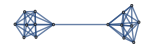
```mathematica
(* Some networks to test and their respective best community partition *)
networks ={-Graphics-,-Graphics-};
bestpartitions = {{1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}};

(* number of testing rounds *)
numbertesting = 100;

(* select a network *)
index = 2;
network = networks⟦index⟧;

(* compute the modularity of the best community partition *)
maxModularity = Fitness[network, bestpartitions⟦index⟧];

(* Print network *)
Print["Size of network: " ,VertexCount[network], " nodes, ", EdgeCount[network], " edges, Number of all possible partitions of this network: ", ScientificForm[BellB[VertexCount[network]]1.0,2]];

MyGraphPlot[network]

(* START TEST *)

(* Lists that hold the number of generations and time needed to find the best community partition, and number of times and chromosomes where it didn't find the best partition *)
generations = {};
times = {};
numberfails = 0;
fails = {};

(* Repeat community detection *)
Do[

(* Find communities *)
{chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time} = FindCommunities[network,numberGenerations->50, matingMethod-> "Elitism"];

(* If successfully found all communities, append number of generations and computation time to list, else increment number of fails and add chromosome to list *)
If[fitnessfittest == maxModularity,
AppendTo[generations, generationfittest];
AppendTo[times, timefittest];
, 
AppendTo[fails, chromosomesfittest⟦-1⟧];
numberfails +=1];

,numbertesting];

(* Print results. Plot all community structures where it failed *)
Print["Time: ", Mean[times], "s ± ", N[StandardDeviation[times]], "s, Generations: ", N[Mean[generations]], " ± ", N[StandardDeviation[generations]],", Max. Generation: ", Max[generations], ", Number fails: ", numberfails];
Manipulate[MyCommunityPlot[network, RelabelChromosome[fails⟦nFails⟧]], {{nFails,numberfails, "Fail No."}, 1, numberfails, 1}]
```

Size of network: 125 nodes, 390 edges, Number of all possible partitions of this network: 2.5×10^153

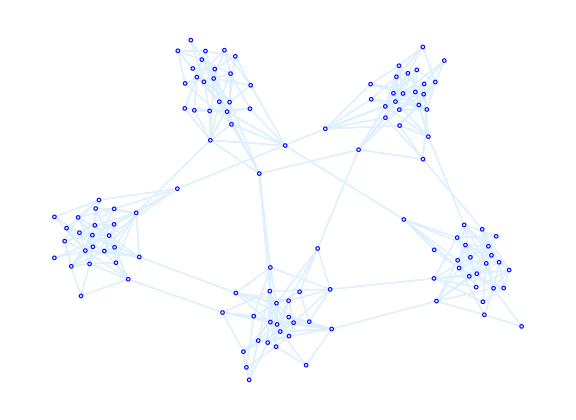

Time: 3.49684s ± 1.89641s, Generations: 8.55789 ± 5.42985, Max. Generation: 30, Number fails: 5

Part::partd: Part specification fails⟦1⟧ is longer than depth of object.

### 2. Network with unknown community structure

Size of network: 1293 nodes, 4145 edges, Number of all possible partitions of this network: 6.7×10^2609

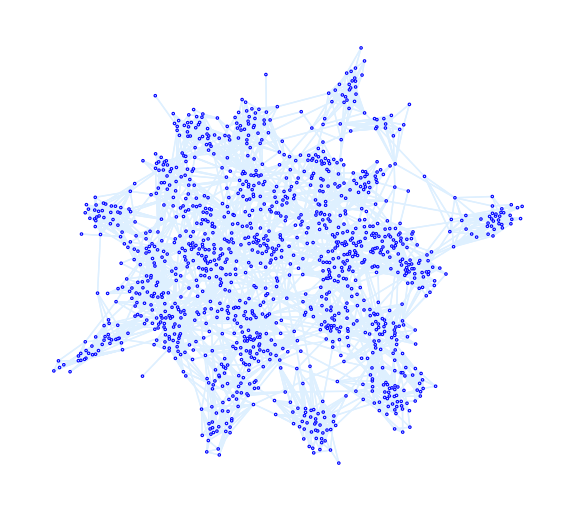

Number of found communities using Mating-method: 38, Generations: 45, Steps: 17, Computation time (until best partition): 826.91s, Computation time (until termination): 1883.78s, Modularity: 0.907236

```mathematica
network = -Graphics-;
(* Find communities *)
Print["Size of network: " ,VertexCount[network], " nodes, ", EdgeCount[network], " edges, Number of all possible partitions of this network: ", ScientificForm[BellB[VertexCount[network]]1.0,2]];
MyGraphPlot[network]
{chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time} = FindCommunities[network,numberGenerations-> 100, matingMethod-> "Mating"];
PrintResults[network, chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time, "Mating"]
```

Number of found communities using built-in function: 43, Modularity: 0.817467

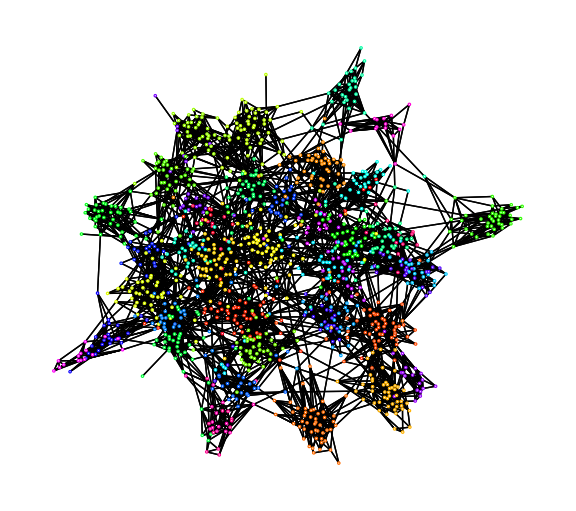

```mathematica
(* Find communities using Mathematica's built-in function *)
partitionbuiltin = FindGraphCommunities[network, Method->"Spectral"];
chromosomebuiltin = PartitionToChromosome[partitionbuiltin];
Print["Number of found communities using built-in function: ", CommunityCount[chromosomebuiltin], ", Modularity: ", N[Fitness[network, chromosomebuiltin]]];
MyCommunityPlot[network,chromosomebuiltin]
```

```mathematica
(* Find distance between two partitions (i.e. number of nodes that must be moved into another community) *)
partition1=ChromosomeToPartition[chromosomesfittest⟦-1⟧];
partition2=partitionbuiltin;

nCommunities1 = Length[partition1];
nCommunities2 = Length[partition2];

(* Create bipartite graph consisting of the two partitions. Use cardinality of intersection of each pair of subgroups as weight *)
(*vertexLabels =Table[i-> ToString[Join[partition1, partition2]⟦i⟧],{i,1,nCommunities1 + nCommunities2}];*)
vertexLabels =Table[i-> i,{i,1,nCommunities1 + nCommunities2}];
bipartiteGraph=CompleteGraph[{nCommunities1,nCommunities2}, EdgeWeight->{v_<->w_ :> Length[partition1⟦v⟧∩partition2⟦w-nCommunities1⟧]}, 
 VertexLabels->vertexLabels, EdgeLabels->Placed["EdgeWeight",1/(nCommunities1+1)]];

(* Find best assignment of the communities *)
assignments = FindIndependentEdgeSet[bipartiteGraph];
(*HighlightGraph[bipartiteGraph,Style[assignments, Red,Thick]]*)

(* Compute partition distance *)
move = Length[Flatten[partition1]] - Total[assignments /. {v_<->w_:>Length[partition1⟦v⟧∩partition2⟦w-nCommunities1⟧]}];
Print["Nodes to be moved: ",move]
```

Nodes to be moved: 143

## Application to various networks

### 1. Two Random Graphs connected

Number of merged graphs: 2, Size of network: 16 nodes, 49 edges, Number of all possible partitions of this network: 1.×10^10

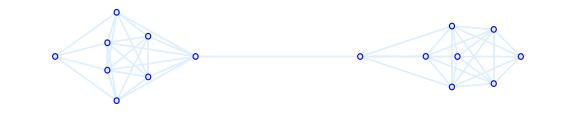

Number of found communities using Elitism-method: 2, Generations: 3, Steps: 3, Computation time (until best partition): 0.14s, Computation time (until termination): 0.17s, Modularity: 0.479592

Number of found communities using Mating-method: 2, Generations: 3, Steps: 3, Computation time (until best partition): 0.15s, Computation time (until termination): 0.2s, Modularity: 0.479592

```mathematica
(* Create two random communities with n nodes and m edges each *)
n=8; m=3n;
network= GraphDisjointUnion@@ Table[RandomGraph[{n,m}],2];

(* Combine them by adding one link between them *)
network = EdgeAdd[network,n/2<->(3n)/2];

(* Find communities *)
Print["Number of merged graphs: 2", ", Size of network: " ,VertexCount[network], " nodes, ", EdgeCount[network], " edges, Number of all possible partitions of this network: ", ScientificForm[BellB[VertexCount[network]]1.0,2]];
MyGraphPlot[network]
{chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time} = FindCommunities[network,numberGenerations->5,matingMethod-> "Elitism"];
PrintResults[network, chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time, "Elitism"]
{chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time} = FindCommunities[network,numberGenerations->5, matingMethod-> "Mating"];
PrintResults[network, chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time, "Mating"]
```

### 2. Five Random Graphs connected

Number of merged graphs: 5, Size of network: 125 nodes, 390 edges, Number of all possible partitions of this network: 2.5×10^153

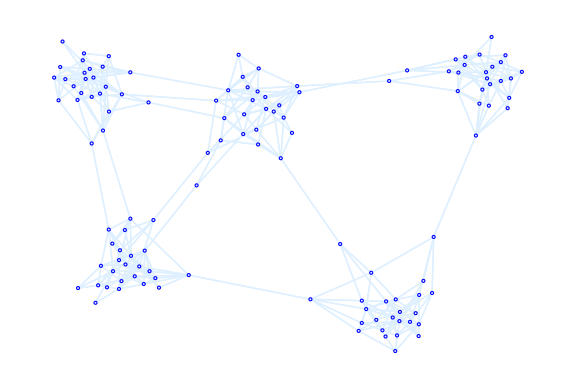

Number of found communities using Elitism-method: 5, Generations: 4, Steps: 4, Computation time (until best partition): 2.06s, Computation time (until termination): 5.76s, Modularity: 0.769038

Number of found communities using Mating-method: 5, Generations: 7, Steps: 7, Computation time (until best partition): 3.s, Computation time (until termination): 5.8s, Modularity: 0.769038

```mathematica
(* Create two random communities with n nodes and m edges each *)
n=25; m=3n;
network= GraphDisjointUnion@@ Table[RandomGraph[{n,m}],5];

(* Combine them by adding links between them *)
Table[{edges =  RandomSample[VertexList[network],2],network = EdgeAdd[network, edges⟦1⟧<->edges⟦2⟧]},15];

(* Find communities *)
Print["Number of merged graphs: 5", ", Size of network: " ,VertexCount[network], " nodes, ", EdgeCount[network], " edges, Number of all possible partitions of this network: ", ScientificForm[BellB[VertexCount[network]]1.0,2]];
MyGraphPlot[network]
{chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time} = FindCommunities[network,numberGenerations->15,matingMethod-> "Elitism"];
PrintResults[network, chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time, "Elitism"]
{chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time} = FindCommunities[network,numberGenerations->15,matingMethod-> "Mating"];
PrintResults[network, chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time, "Mating"]
```

### 3. Many Random Graphs connected

Number of merged graphs: 14, Size of network: 284 nodes, 894 edges, Number of all possible partitions of this network: 3.7×10^424

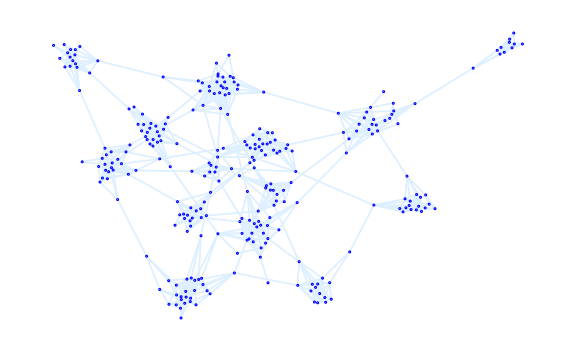

Number of found communities using Elitism-method: 14, Generations: 6, Steps: 6, Computation time (until best partition): 10.21s, Computation time (until termination): 35.79s, Modularity: 0.878852

Number of found communities using Mating-method: 13, Generations: 8, Steps: 8, Computation time (until best partition): 11.48s, Computation time (until termination): 33.59s, Modularity: 0.845278

```mathematica
(* Create a few RandomGraphs communities of random size *)
n:=RandomInteger[{10,30}]; a=RandomInteger[{10,30}];
network = GraphDisjointUnion@@ Table[RandomGraph[n{1,3}],a];

(* Combine them by randomly adding some links between them *)
Table[{edges =  RandomSample[VertexList[network],2],network = EdgeAdd[network, edges⟦1⟧<->edges⟦2⟧]},3a];

(* Find communities *)
Print["Number of merged graphs: ",a, ", Size of network: " ,VertexCount[network], " nodes, ", EdgeCount[network], " edges, Number of all possible partitions of this network: ", ScientificForm[BellB[VertexCount[network]]1.0,2]];
MyGraphPlot[network]
{chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time} = FindCommunities[network,numberGenerations-> 25, matingMethod-> "Elitism"];
PrintResults[network, chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time, "Elitism"]
{chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time} = FindCommunities[network,numberGenerations-> 25, matingMethod-> "Mating"];
PrintResults[network, chromosomesfittest, fitnessfittest, generationfittest, timefittest, maxfitness, meanfitness, time, "Mating"]
```